```mathematica
SetDirectory["C:\\Users\\nemes\\OneDrive\\Documents\\Academics\\UChicago\\Research\\ACA-MTD"];
```

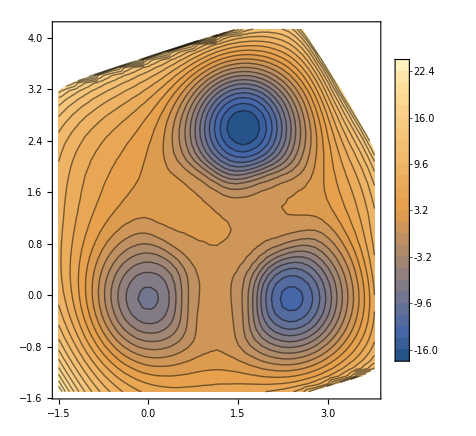

-Graphics3D-

```mathematica
domain={{-1.5,4},{-1.5,4.5}};
gridsize=50;
data=ArrayReshape[ToExpression[StringSplit[ReadList["gaussian_cv.txt",String],{" ","[","]"}][[53]]],{gridsize-1,gridsize-1}];
ListContourPlot[Flatten[Table[
{(i-1)(domain[[1,2]]-domain[[1,1]])/gridsize+domain[[1,1]],(j-1)(domain[[2,2]]-domain[[2,1]])/gridsize+domain[[2,1]],data[[i,j]]},
{i,gridsize-1},{j,gridsize-1}
],1],PlotRange->All,Contours->25,PlotLegends->Automatic,AspectRatio->(domain[[2,2]]-domain[[2,1]])/(domain[[1,2]]-domain[[1,1]])]
ListPlot3D[Flatten[Table[
{(i-1)(domain[[1,2]]-domain[[1,1]])/gridsize+domain[[1,1]],(j-1)(domain[[2,2]]-domain[[2,1]])/gridsize+domain[[2,1]],data[[i,j]]},
{i,gridsize-1},{j,gridsize-1}
],1],PlotRange->All,ImageSize->Large]
```

```mathematica
large1={1.0,0.0,0.0,-1.0};
large2={-1.0,-1.0,1.0,-1.0};
large3={-1.0,-1.0,-1.0,1.0};
max1={1/3,-2/3,2/3,-1.0};
max2={-1/3,-2/3,-2/3,1/3};
max3={-1.0,-1.0,1/3,-1/3};
max4={-1/3,-2/3,0,-1/3};
v12=large2-large1;
v12=v12/Norm[v12]
v13=large3-large1;
v13=v13-v13.v12/Norm[v12]^2*v12;
v13=v13/Norm[v13]
```

{-0.816497,-0.408248,0.408248,0.}

{-0.246183,-0.123091,-0.615457,0.738549}

```mathematica
x[x1_,x2_,x3_,x4_]=({x1,x2,x3,x4}-large1).v12//Expand
y[x1_,x2_,x3_,x4_]=({x1,x2,x3,x4}-large1).v13//Expand
```

0.816497-0.816497 x1-0.408248 x2+0.408248 x3

0.984732-0.246183 x1-0.123091 x2-0.615457 x3+0.738549 x4

```mathematica
{xs,ys}={x[-1,-1,-1,1],y[-1,-1,-1,1]}
```

{1.63299,2.70801}

```mathematica
cmapdensity=Blend[{RGBColor[{255,247,243}/255],RGBColor[{145,0,63}/255]},Tanh[2#]]&;
```

```mathematica
{xi,xf,dx}={0.18389026164310862,3.2756050002289454,0.012124371523866027};
{yi,yf,dy}={1.153693633200726,4.1663346618664185,0.01181427854378703};
nbins=256;
kde=ToExpression[StringSplit[StringReplace[ReadList["kde.out",String],{"e+":>"*^","e-":>"*^-"}]]];
kde=Chop[kde];
fes=-Log[kde];
ListContourPlot[Flatten[Table[{xi+i dx,yi+j dy,kde[[i,j]]},{i,nbins},{j,nbins}],1],
ColorFunction->cmapdensity,ColorFunctionScaling->False,PlotLegends->Placed[Automatic,Right],PlotRange->Full,Contours->10,AspectRatio->(yf-yi)/(xf-xi)]
```

-Graphics-

```mathematica
ListContourPlot[Flatten[Table[{xi+i dx,yi+j dy,fes[[i,j]]},{i,nbins},{j,nbins}],1],PlotLegends->Placed[Automatic,Right],PlotRange->Full,Contours->10,AspectRatio->(yf-yi)/(xf-xi)]
```

-Graphics-

```mathematica
ListPlot3D[Flatten[Table[{xi+i dx,yi+j dy,fes[[i,j]]},{i,nbins},{j,nbins}],1],PlotRange->Full]
```

-Graphics3D-

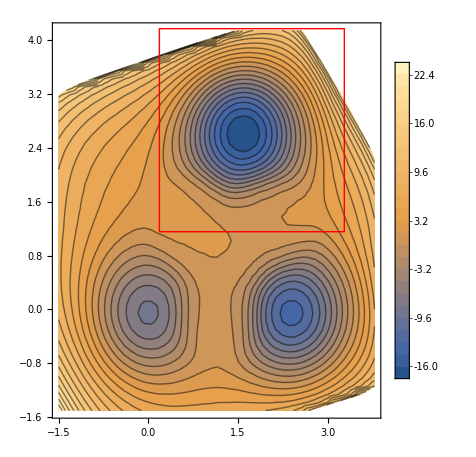

```mathematica
Show[
data=ArrayReshape[ToExpression[StringSplit[ReadList["gaussian_cv.txt",String],{" ","[","]"}][[53]]],{gridsize-1,gridsize-1}];
ListContourPlot[Flatten[Table[
{(i-1)(domain[[1,2]]-domain[[1,1]])/gridsize+domain[[1,1]],(j-1)(domain[[2,2]]-domain[[2,1]])/gridsize+domain[[2,1]],data[[i,j]]},
{i,gridsize-1},{j,gridsize-1}
],1],PlotRange->All,Contours->25,PlotLegends->Automatic,AspectRatio->(4.1+1.5)/(3.4+1.5)],
Graphics[{Red,Line[{{xi,yi},{xf,yi},{xf,yf},{xi,yf},{xi,yi}}]}]
]
```

```mathematica
res1=ToExpression[StringSplit[StringReplace[ReadList["res1.out",String],{"e+":>"*^","e-":>"*^-"}]]];
res1=Chop[res1];
fes=-Log[res1];
ListContourPlot[Flatten[Table[{xi+i dx,yi+j dy,res1[[i,j]]},{i,nbins},{j,nbins}],1],
ColorFunction->cmapdensity,ColorFunctionScaling->False,PlotLegends->Placed[Automatic,Right],PlotRange->Full,Contours->10,AspectRatio->(yf-yi)/(xf-xi)]
```

-Graphics-

```mathematica
ListContourPlot[Flatten[Table[{xi+i dx,yi+j dy,fes[[i,j]]},{i,nbins},{j,nbins}],1],PlotLegends->Placed[Automatic,Right],PlotRange->Full,Contours->10,AspectRatio->(yf-yi)/(xf-xi)]
```

-Graphics-

```mathematica
ListPlot3D[Flatten[Table[{xi+i dx,yi+j dy,fes[[i,j]]},{i,nbins},{j,nbins}],1],PlotRange->Full,AspectRatio->(yf-yi)/(xf-xi)]
```

-Graphics3D-

```mathematica
xs
ys
```

1.63299

2.70801

```mathematica
xi+248dx
yi+258dy
```

1.62566

2.70215

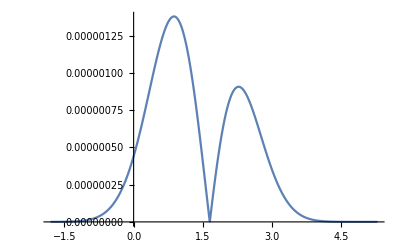

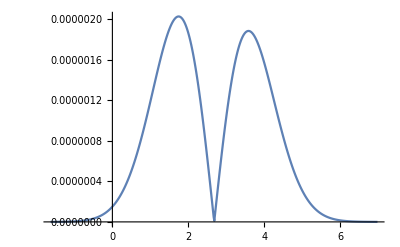

```mathematica
ListPlot[Table[{xi+i dx,res1[[i,258]]},{i,nbins}],Joined->True]
ListPlot[Table[{yi+j dy,res1[[248,j]]},{j,nbins}],Joined->True]
```

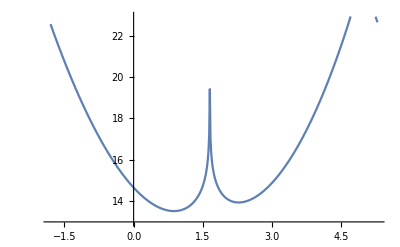

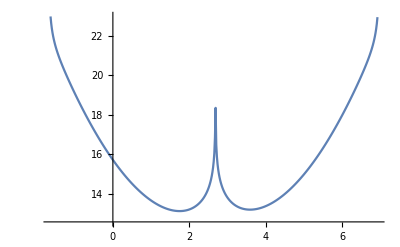

```mathematica
ListPlot[Table[{xi+i dx,fes[[i,258]]},{i,nbins}],Joined->True]
ListPlot[Table[{yi+j dy,fes[[248,j]]},{j,nbins}],Joined->True]
```

```mathematica
densadj=res1(kde+1.*^-20)^-1;
Vbias=-Log[densadj];
ListContourPlot[Flatten[Table[{xi+i dx,yi+j dy,Vbias[[i,j]]},{i,nbins},{j,nbins}],1],PlotLegends->Automatic,Contours->5(*,AspectRatio->(3.5-2.2)/(2.5-0.8)*)]
ListPlot3D[Flatten[Table[{xi+i dx,yi+j dy,Vbias[[i,j]]},{i,nbins},{j,nbins}],1](*,AspectRatio->(3.5-2.2)/(2.5-0.8)*),PlotRange->All]
```

-Graphics-

-Graphics3D-

```mathematica
densadj=res1;
Vbias=-Log[densadj]-15;
cutoff=1.*^-5;
Do[If[kde[[i,j]]<cutoff,Vbias[[i,j]]=0.],{i,nbins},{j,nbins}]
ListContourPlot[Flatten[Table[{xi+i dx,yi+j dy,Vbias[[i,j]]},{i,nbins},{j,nbins}],1],PlotLegends->Automatic,Contours->5(*,AspectRatio->(3.5-2.2)/(2.5-0.8)*)]
ListPlot3D[Flatten[Table[{xi+i dx,yi+j dy,Vbias[[i,j]]},{i,nbins},{j,nbins}],1](*,AspectRatio->(3.5-2.2)/(2.5-0.8)*),PlotRange->All]
```

-Graphics-

-Graphics3D-

```mathematica
{xi,xf,dx}={-1.8161097383568912,5.275605000228945,0.013878111034414553};
{yi,yf,dy}={-1.6463063667992741,6.966334661866419,0.016854483422046367};
nbins=512;
res2=ToExpression[StringSplit[StringReplace[ReadList["res2.out",String],{"e+":>"*^","e-":>"*^-"}]]];
res2=Chop[res2];
fes=-Log[res2];
ListContourPlot[Flatten[Table[{xi+i dx,yi+j dy,res2[[i,j]]},{i,nbins},{j,nbins}],1],
ColorFunction->cmapdensity,ColorFunctionScaling->False,PlotLegends->Automatic,PlotRange->{domain[[1]],domain[[2]],Full},Contours->10(*,AspectRatio->(4.1+1.5)/(3.4+1.5)*)]
```

-Graphics-

```mathematica
ListContourPlot[Flatten[Table[{xi+i dx,yi+j dy,fes[[i,j]]},{i,nbins},{j,nbins}],1],PlotLegends->Automatic,PlotRange->{domain[[1]],domain[[2]],Full},Contours->10(*,AspectRatio->(3.5-2.2)/(2.5-0.8)*)]
```

-Graphics-

```mathematica
ListPlot3D[Flatten[Table[{xi+i dx,yi+j dy,fes[[i,j]]},{i,nbins},{j,nbins}],1],PlotRange->{domain[[1]],domain[[2]],Full}(*,AspectRatio->(3.5-2.2)/(2.5-0.8)*)]
```

-Graphics3D-

```mathematica
(*densadj=res1(kde+1.*^-20)^-0.3;
densadj=Chop[densadj];*)
densadj=res1;
Vbias=-Log[densadj];
cutoff=1.*^-5;
Do[If[kde[[i,j]]<cutoff,Vbias[[i,j]]=0.],{i,256},{j,256}]
ListContourPlot[Flatten[Table[{xi+i dx,yi+j dy,Vbias[[i,j]]},{i,256},{j,256}],1],PlotLegends->Automatic,Contours->5,AspectRatio->(3.5-2.2)/(2.5-0.8)]
ListPlot3D[Flatten[Table[{xi+i dx,yi+j dy,Vbias[[i,j]]},{i,256},{j,256}],1],AspectRatio->(3.5-2.2)/(2.5-0.8),PlotRange->All]
```

-Graphics-

-Graphics3D-

```mathematica
{xi,xf,dx}={0.8119808494874291,2.5321276069578134,0.006745673558707389};
{yi,yf,dy}={2.1733229207094564,3.4985603526920244,0.005197009537186541};
dens=ToExpression[StringSplit[StringReplace[ReadList["res2.out",String],{"e+":>"*^","e-":>"*^-"}]]];
ListContourPlot[Flatten[Table[{xi+i dx,yi+j dy,dens[[i,j]]},{i,256},{j,256}],1],
ColorFunction->cmapdensity,ColorFunctionScaling->False,PlotRange->All,Contours->6,AspectRatio->(3.5-2.2)/(2.5-0.8)]
```

-Graphics-

```mathematica
{xi,xf,dx}={0.8119808494874291,2.5321276069578134,0.006745673558707389};
{yi,yf,dy}={2.1733229207094564,3.4985603526920244,0.005197009537186541};
dens=ToExpression[StringSplit[StringReplace[ReadList["res3.out",String],{"e+":>"*^","e-":>"*^-"}]]];
ListContourPlot[Flatten[Table[{xi+i dx,yi+j dy,dens[[i,j]]},{i,256},{j,256}],1],
ColorFunction->cmapdensity,ColorFunctionScaling->False,PlotRange->All,Contours->5,AspectRatio->(3.5-2.2)/(2.5-0.8)]
```

-Graphics-

```mathematica
{xi,xf,dx}={0.8119808494874291,2.5321276069578134,0.006745673558707389};
{yi,yf,dy}={2.1733229207094564,3.4985603526920244,0.005197009537186541};
dens=ToExpression[StringSplit[StringReplace[ReadList["res4.out",String],{"e+":>"*^","e-":>"*^-"}]]];
ListContourPlot[Flatten[Table[{xi+i dx,yi+j dy,dens[[i,j]]},{i,256},{j,256}],1],
ColorFunction->cmapdensity,ColorFunctionScaling->False,PlotRange->All,Contours->4,AspectRatio->(3.5-2.2)/(2.5-0.8)]
```

-Graphics-

```mathematica
{xi,xf,dx}={0.8119808494874291,2.5321276069578134,0.006745673558707389};
{yi,yf,dy}={2.1733229207094564,3.4985603526920244,0.005197009537186541};
dens=ToExpression[StringSplit[StringReplace[ReadList["res5.out",String],{"e+":>"*^","e-":>"*^-"}]]];
ListContourPlot[Flatten[Table[{xi+i dx,yi+j dy,dens[[i,j]]},{i,256},{j,256}],1],
ColorFunction->cmapdensity,ColorFunctionScaling->False,PlotRange->All,Contours->3,AspectRatio->(3.5-2.2)/(2.5-0.8)]
```

-Graphics-